# Reverse Dictionary

## Data

Data was taken from the site of the following paper: Hill, F. Cho, KH., Korhonen, A., and Bengio, Y. Learning to Understand Phrases by Embedding the Dictionary. 2016. Transactions of the Association for Computational Linguistics (TACL). Originally it was recollected via WordNik API in Python.

## Proof of Concept

For this first proof of concept analysis, we used 50 of the most common nouns in the English language. We chose the 50 with more definitions assigned to them so that the training can be more efficient. The number of definitions per word was normalized to the minimum among the maximum number of definitions for each word. This was so there would be no bias in the data.

Global Set

```mathematica
wordDefSet={};
```

```mathematica
stext=OpenRead["Personal\\WSS\\wss_project\\training_data\\60Def50Words.csv"];
```

```mathematica
l=StringSplit[Read[stext,Record,RecordSeparators->{"\n"}],", "];
While[Not[SameQ[First[l],EndOfFile]],
AppendTo[wordDefSet,Last[l]-> First[l]];
l=StringSplit[Read[stext,Record,RecordSeparators->{"\n"}],", "];
]//Quiet
```

```mathematica
Close[stext];
```

```mathematica
RandomSample[wordDefSet, 10]//TableForm
```

offering services to the public in response to need or demand a service industry→service
law an action or a suit or just grounds for an action→case
computer science a starting position within a computer application such as the beginning of a line file or screen or the top of a chart or list→home
the stiff and attentive stance taken by a hunting dog→point
the list of current buy and sell orders maintained by a stock market specialist→book
a unit of angular distance equal to a of a degree→minute
the act of passing or flowing out a moving out from any inclosed place egress→issue
to consider attentively to examine closely→study
the title of a senator in ancient rome→father
good word a favorable comment she put in a good word for me→word

Testing Set

```mathematica
testingSet=Normal[DeleteDuplicates[Association[RandomSample[wordDefSet]]]];
RandomSample[testingSet, 10]//TableForm
```

to indicate the presence and position of game by standing immobile and directing the muzzle toward it→point
printing a typeface or range of typefaces→face
a unit of angular measurement equal to one sixtieth of a degree or seconds→ï»¿minute
a share of a responsibility or obligation your end of the bargain→end
voting is one way to elect a president→president
a functional entity consisting of certain atoms whose presence provides a certain property to a molecule such as the methyl group→group
the body of rules and standards issued by a government or to be applied by courts and similar authorities→law
in such frameworks nouns in english have case even in the absence of inflectional case endings→case
informal of or relating to influential business or professional practices a pinstriped suit with a power tie met with high level executives at a power breakfast→power
to fortify or brace manned himself for the battle ahead→man

Training Set

```mathematica
trainingSet=Select[wordDefSet,Not[MemberQ[testingSet,First[#]->_]]&];
RandomSample[trainingSet, 10]
```

{the total number of points required to win a game one hundred points is game in bridge→game,a pursuit or activity with rules performed either alone or with others for the purpose of entertainment→game,to total or count to amount to→number,the period between dusk and midnight of a given day either late thursday night or early friday morning→night,the opposite of night is day→night,to make fit for use adjust repair or maintain service a car→service,one s facial expression→face,something suggestive of the vertebrate organ of vision especially→eye,that which one has to do or should do special service duty or mission→business,a floor of a multi storey building→level}

Simplest Approach

Simplest Approach consists of using built in function Classify to attempt to solve the problem.

```mathematica
cl=Classify[trainingSet,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[cl,testingSet]
```

ClassifierMeasurementsObject[…]

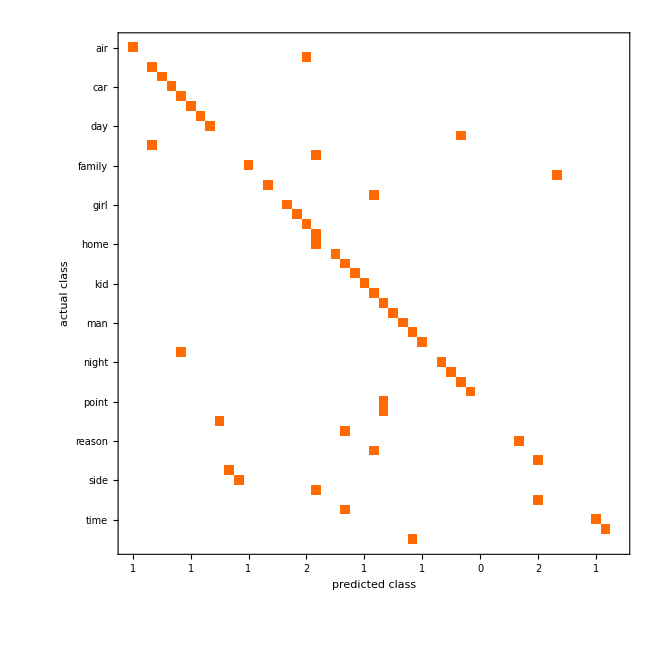

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
ClassifierInformation[cl]
```

Classifier information
Method | Markov
Number of classes | 50
Number of features | 1
Number of training examples | 2942
Number of tokens | 5682
Markov order | 1
Regularization method | Katz

Apparently this does it, and the performance seems pretty good. Now, this model might be over-fitted, so we must test with data it has never seen.

```mathematica
ClassifierMeasurements[cl,testingSet,"Accuracy"]
```

0.627451

```mathematica
ClassifierMeasurements[cl,testingSet,"F1Score"]
```

<|air→1.,back→0.,book→0.666667,business→1.,car→1.,case→0.666667,change→1.,company→1.,day→1.,end→0.,eye→0.,face→0.,family→1.,father→0.,force→1.,game→0.,girl→1.,group→1.,hand→0.666667,head→0.5,home→0.,house→0.666667,issue→0.5,job→1.,kid→1.,law→0.5,level→0.5,lot→1.,man→1.,minute→0.666667,mother→1.,name→0.,night→1.,number→1.,part→0.666667,party→1.,point→0.,power→0.,president→0.,question→0.,reason→1.,right→0.,school→0.666667,service→0.,side→0.,state→0.,study→0.,thing→0.,time→1.,word→1.,ï»¿minute→0.|>

Test with own definitions

```mathematica
cl[{
"Motorized vehicle used for transportation",
"Basic unit of written communication",
"Value used to express quantity or amount",
"Human child",
"A young person",
"Defined by past, present and future",
"Breathable oxygen dispersed throughout earth's atmosphere"
},
"TopProbabilities"]//TableForm
```

car→0.999173 |  | 
word→0.960848 |  | 
number→0.693759 | lot→0.228681 | 
girl→0.713115 | man→0.169508 | mother→0.112618
girl→0.665144 | kid→0.334663 | 
time→0.999474 |  | 
air→0.860834 | mother→0.135671 |

## Complete Data Set

Training Set

```mathematica
rawData=Import["Personal\\WSS\\wss_project\\training_data\\training_data.csv"]
```

{{fawn, to exhibit affection or attempt to please as a dog does by wagging its tail whining or cringing},{fawn, to seek favor or attention by flattery and obsequious behavior},{fawn, a young deer especially one less than a year old},{fawn, a grayish yellow brown to moderate reddish brown},852464,{jawbone, any bone of the jaws as a maxillary or mandibular bone especially a bone of the lower jaw},{jawbone, talk idly or casually and in a friendly way},{jawbone, the jaw in vertebrates that is hinged to open the mouth}}
 |  |  |  |

```mathematica
associate[elem_]:=Last[elem]-> First[elem];
```

```mathematica
trainingSet=Map[associate, rawData]
```

{ to exhibit affection or attempt to please as a dog does by wagging its tail whining or cringing→fawn, to seek favor or attention by flattery and obsequious behavior→fawn, a young deer especially one less than a year old→fawn, a grayish yellow brown to moderate reddish brown→fawn,852463, to make public appeals in order to influence the behavior of businessmen or labor leaders used especially of the president or other high government officials→jawbone, any bone of the jaws as a maxillary or mandibular bone especially a bone of the lower jaw→jawbone, talk idly or casually and in a friendly way→jawbone, the jaw in vertebrates that is hinged to open the mouth→jawbone}
 |  |  |  |

Testing Set

```mathematica
rawTesting=Import["Personal\\WSS\\wss_project\\test_data\\testing_data.csv"];
```

```mathematica
testingSet=Map[associate, rawTesting];
RandomSample[testingSet, 10]//TableForm
```

a plain tasting root vegetable used as a staple food and to make chips or fries→potato
 a person in a hospital who is unwell and being treated by doctors or nurses→patient
 the possibility or chance of doing or achieving something positive→opportunity
 a particular way of doing something→method
 when a living thing gets bigger naturally→grow
 the substance that emerges from a fire when wood is burned→smoke
 a place like a large town where many people live close together →city
 the process where the price of things increases across a country or economy→inflation
 a popular alcoholic drink made with grapes→wine
 the fuel that people put in their cars→petrol

Simplest Approach

```mathematica
cl=Classify[trainingSet]
```